```mathematica
tri [x_]:=Piecewise[{{1-Abs[x],Abs[x]<1},{0,Abs[x]≥1}}]
boxcar[x_]:=Piecewise[{{1,1≥x≥0},{0, x<0||x>1}}]
gaussian[x_]:=(1/(2Pi))^.5*Exp[-x^2/2]
```

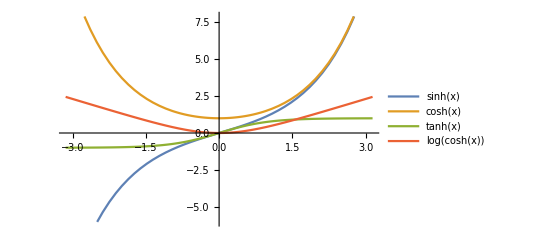

```mathematica
Plot[{Sinh[x],Cosh[x], Tanh[x],Log[Cosh[x]]},{x,-Pi,Pi}, PlotLegends->"Expressions"]
```

```mathematica
FullSimplify[Integrate[-Tanh[x],x]]
```

-Log[Cosh[x]]

### 5.(2)(a)

```mathematica
u52a[x_,t_]:=1/2(tri[x+3t]+tri[x-3t])
Manipulate[Plot[u52a[x,t],{x,-5,5}, PlotRange->{0,2}],{t,0,2}]
```

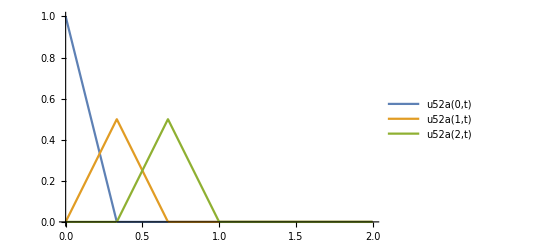

```mathematica
Plot[{u52a[0,t],u52a[1,t],u52a[2,t]},{t,0,2}, PlotRange->{0,1}, PlotLegends->"Expressions"]
```

### 5.(2)(b)

```mathematica
u52b[x_,t_]:=1/2∫_(x-3t)^(x+3t) Cos[s]ⅆs;
```

```mathematica
Manipulate[Plot[u52b[x,t],{x,-5,5}, PlotRange->{-1,1}],{t,0,2}]
```

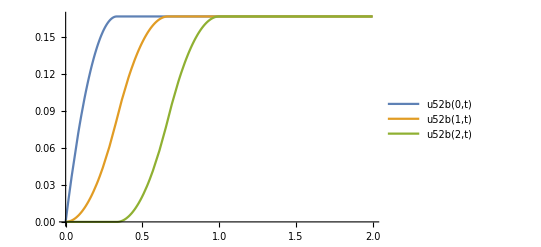

```mathematica
Plot[{u52b[0,t],u52b[1,t],u52b[2,t]},{t,0,2}, PlotRange->Automatic, PlotLegends->"Expressions"]
```

### 5.(2)(c)

```mathematica
u52c[x_,t_]:=1/2(Sin[5x+5t]-Sin[5x-5t]);
```

```mathematica
Manipulate[Plot[u52c[x,t],{x,-5,5}, PlotRange->{-2,2}],{t,0,5}]
```

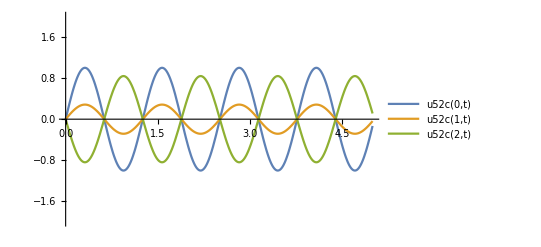

```mathematica
Plot[{u52c[0,t],u52c[1,t],u52c[2,t]},{t,0,5}, PlotRange->{-2,2}, PlotLegends->"Expressions"]
```

### 5.(2)(d)

```mathematica
u52d[x_,t_]:=1/2(Sin[x+5t]-Sin[x-5t]);
```

```mathematica
Manipulate[Plot[u52d[x,t],{x,-5,5}, PlotRange->{-2,2}],{t,0,5}]
```

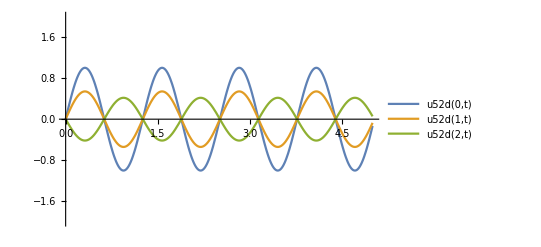

```mathematica
Plot[{u52d[0,t],u52d[1,t],u52d[2,t]},{t,0,5}, PlotRange->{-2,2}, PlotLegends->"Expressions"]
```

### 6.(1)a

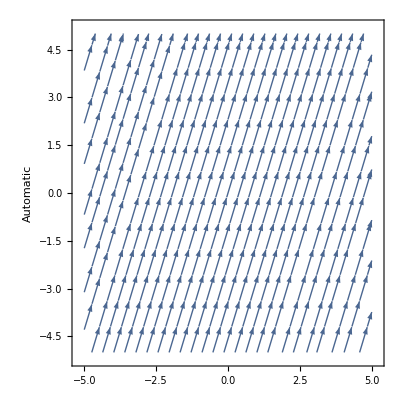

```mathematica
StreamPlot[{1,3},{t,-5,5},{x,-5,5},AxesLabel->Automatic]
```

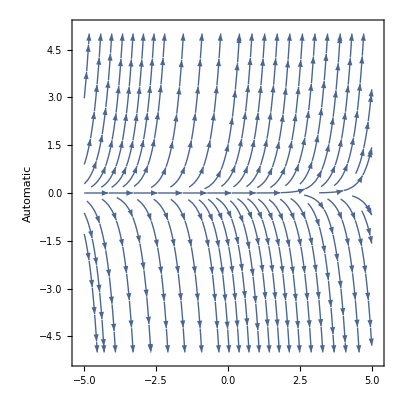

```mathematica
StreamPlot[{1,3x},{t,-5,5},{x,-5,5},AxesLabel->Automatic]
```

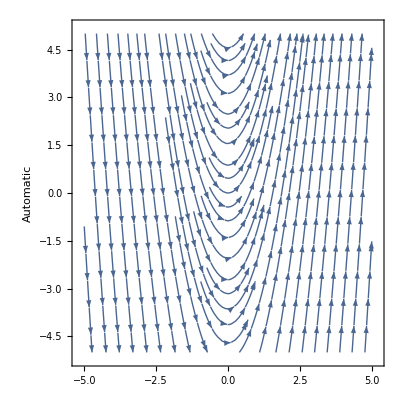

```mathematica
StreamPlot[{1,3t},{t,-5,5},{x,-5,5},AxesLabel->Automatic]
```

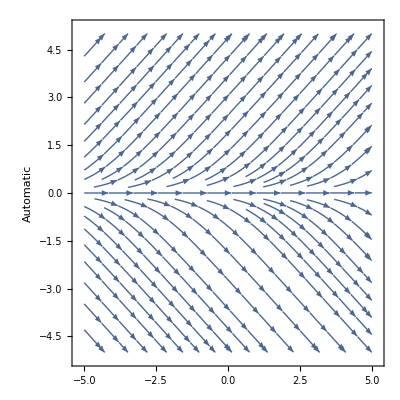

```mathematica
StreamPlot[{1,Tanh[x]},{t,-5,5},{x,-5,5},AxesLabel->Automatic]
```

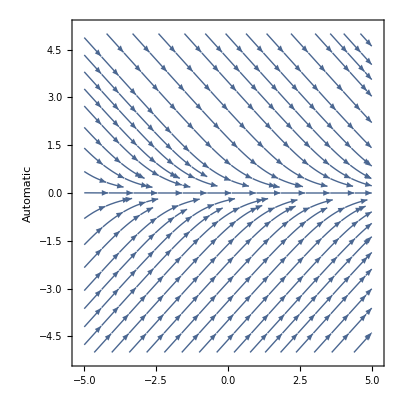

```mathematica
StreamPlot[{1,-Tanh[x]},{t,-5,5},{x,-5,5},AxesLabel->Automatic]
```

#### 6. (1)f+g

-Graphics3D-

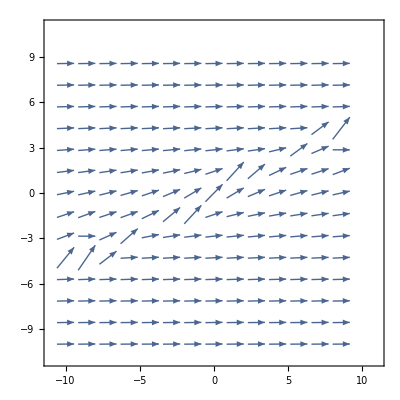

```mathematica
s=NDSolve[{D[u[t,x],t]+u[t,x]*D[u[t,x],x]==0,u[0,x]==1/(1+x^2)},u,{t,-10,10},{x,-10,10}];
Plot3D[Evaluate[u[t,x]/.s],{t,-10,10},{x,-10,10}, PlotRange->All, AxesLabel->{t,x,u}]
VectorPlot[{1,Evaluate[u[t,x]/.s]},{t,-10,10},{x,-10,10}]
```

-Graphics3D-

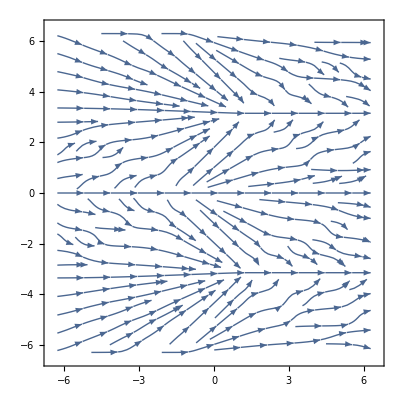

```mathematica
g=NDSolve[{D[u[t,x],t]+u[t,x]*D[u[t,x],x]==0,u[0,x]==Sin[x]},u,{t,-2Pi,2Pi},{x,-2Pi,2Pi}];
Plot3D[Evaluate[u[t,x]/.g],{t,-2Pi,2Pi},{x,-2Pi,2Pi}, PlotRange->All, AxesLabel->{t,x,u}]
StreamPlot[{1,Evaluate[u[t,x]/.g]},{t,-2Pi,2Pi},{x,-2Pi,2Pi}]
```

### 6(3)

```mathematica
eqn = D[u[t,x],t]+3*D[u[t,x],x]==0;
ic = {u[0,x]==tri[x]};
```

```mathematica
u63a=DSolve[{ D[u[t,x],t]+3D[u[t,x],x]==0,u[0,x]==tri[x]},u,{t,x}];
```

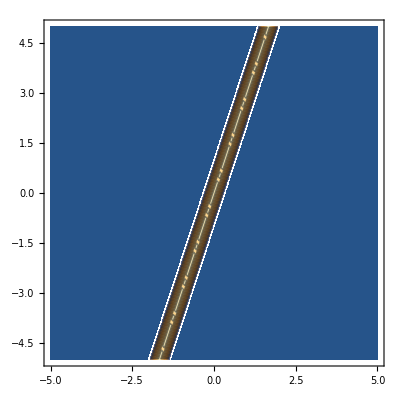

```mathematica
ContourPlot[Evaluate[u[t,x]/.u63a],{t,-5,5},{x,-5,5},PerformanceGoal->"Quality"]
```

```mathematica
Plot3D[Evaluate[u[t,x]/.u63a],{t,-5,5},{x,-5,5},PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
u63b=NDSolve[{D[u[t,x],t]+x*D[u[t,x],x]==0,u[0,x]==tri[x]},u,{t,0,5},{x,-Exp[5],Exp[5]}];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

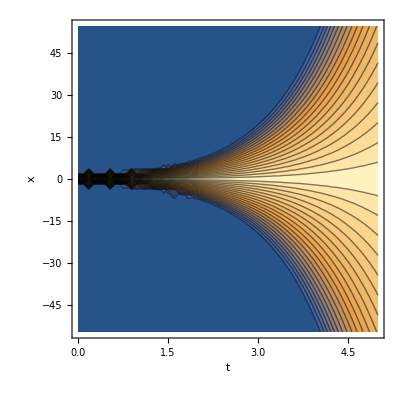

```mathematica
ContourPlot[Evaluate[u[t,x]/.u63b],{t,0,5},{x,-Exp[4],Exp[4]},PerformanceGoal->"Quality",AxesLabel->{t,x},Contours->20]
```

```mathematica
Plot3D[Evaluate[u[t,x]/.u63b],{t,0,5},{x,-Exp[5],Exp[5]},PerformanceGoal->"Quality",AxesLabel->{t,x},PlotRange->Full]
```

-Graphics3D-

```mathematica
u63c=NDSolve[{D[u[t,x],t]+Tanh[x]*D[u[t,x],x]==0,u[0,x]==tri[x]},u,{t,0,10},{x,-10,10}];
```

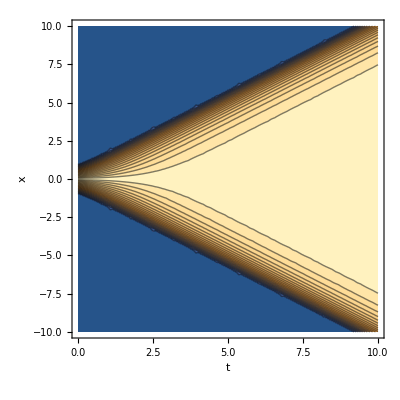

```mathematica
ContourPlot[Evaluate[u[t,x]/.u63c],{t,0,10},{x,-10,10},PerformanceGoal->"Quality",AxesLabel->{t,x},Contours->20]
```

```mathematica
u63d=NDSolve[{D[u[t,x],t]-Tanh[x]*D[u[t,x],x]==0,u[0,x]==tri[x]},u,{t,-10,0},{x,-10,10}];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

NDSolve::eerr: Warning: scaled local spatial error estimate of 1068.73 at t = -10. in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 10001 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

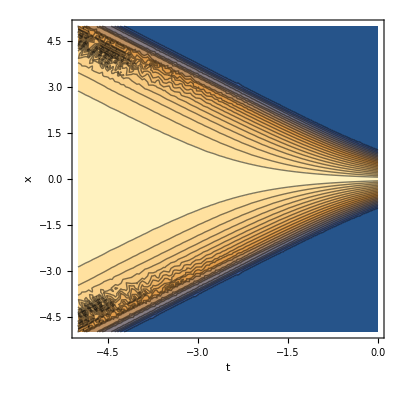

```mathematica
ContourPlot[Evaluate[u[t,x]/.u63d],{t,-5,0},{x,-5,5},PerformanceGoal->"Quality",AxesLabel->{t,x},Contours->20]
```

```mathematica
u63e=NDSolve[{D[u[t,x],t]+u[t,x]*D[u[t,x],x]==0,u[0,x]==tri[x]},u,{t,-5,5},{x,-5,5}];
```

NDSolve::ndsz: At t == 2.40115, step size is effectively zero; singularity or stiff system suspected.

NDSolve::eerr: Warning: scaled local spatial error estimate of 4.28858×10^8 at t = -1.02179 in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 10001 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

NDSolve::eerr: Warning: scaled local spatial error estimate of 1.13847×10^10 at t = 2.40115 in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 10001 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

```mathematica
Plot3D[Evaluate[u[t,x]/.u63e],{t,-1,1},{x,-2,2},PerformanceGoal->"Quality",AxesLabel->{t,x},Contours->20]
```

-Graphics3D-

### 7(2) Visualization

```mathematica
u[t_]:=Exp[-5t]+Exp[-5t]*Integrate[tri[x]*Exp[5x],{x,0, t}]
```

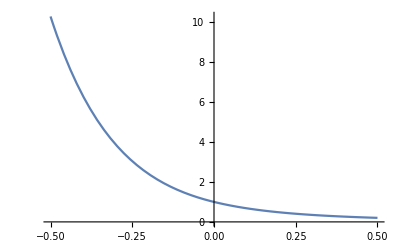

```mathematica
Plot[u[t], {t,-.5, .5}]
```

```mathematica
xi[x_,t_]:= x+5t; tau[x_,t_]:=x-5t;
u7c[xi1_,tau1_]:=1/10 tri[xi1]*tau1;
```

```mathematica
Plot3D[u7c[xi[x,t],tau[x,t]],{t,-1, 1},{x,-1,1}]
```

-Graphics3D-

```mathematica
alpha[x_,t_]:= x-5t;beta[x_,t_]:=5x+t;
u7cbrandon[a_,b_]:=1/26 tri[a]*b;
```

### 8(1) Scaling

```mathematica
Manipulate[Plot[{boxcar[x],2boxcar[x/2],5boxcar[x/5],10boxcar[x/10],50boxcar[x/50],100boxcar[x/100]},{x,-1,200},PlotLegends->"Expressions",PlotRange->{{0,h}, {0,h}}],{h,2,125}]
```

```mathematica
Manipulate[Plot[{tri[x],2tri[x/2],5tri[x/5],10tri[x/10],50tri[x/50],100tri[x/100]},{x,-100,100},PlotLegends->"Expressions",PlotRange->{{-h,h}, {0,h}}],{h,2,125}]
```

```mathematica
Manipulate[Plot[{gaussian[x],2^.5*gaussian[x/2],5^.5*gaussian[x/5],10^.5*gaussian[x/10],50^.5*gaussian[x/50],100^.5*gaussian[x/100]},{x,-300,300},PlotLegends->"Expressions",PlotRange->{{-1.8^h,1.8^h}, {0,h/2}}],{h,2,10}]
```